```mathematica
data={(*{"T"," J"," B"," D"," E"," M_x"," M_y"," M_z"," C"," X"," SD"},*){0,1,0,0,-4857.04,-174.681,-58.7293,-95.1055,0.0648093,0.974393,40.353},{0.01,1,0,0,-4861.62,-350.002,-284.31,-59.4915,0.0772357,0.876822,-2.3009},{0.02,1,0,0,-4845.2,283.871,108.236,173.14,0.108826,0.927187,-0.548409},{0.03,1,0,0,-4840.04,19.5783,173.151,-472.79,0.0962479,0.848812,-123.221},{0.04,1,0,0,-4797.05,-87.2329,234.702,-566.118,0.117619,0.771843,75.1356},{0.05,1,0,0,-4834.96,236.467,-2.16612,219.711,0.0829408,0.937943,-1.05183},{0.06,1,0,0,-4832.88,-20.8075,-79.2376,-321.988,0.0869141,0.934237,42.4383},{0.07,1,0,0,-4827.49,-399.99,316.832,-106.989,0.0861998,0.838139,-1.18361},{0.08,1,0,0,-4802.95,-113.474,-331.448,-483.464,0.086796,0.787744,38.9259},{0.09,1,0,0,-4775.25,564.726,20.1482,114.193,0.0964619,0.802096,37.6344},{0.1,1,0,0,-4787.98,-174.736,417.208,-479.509,0.0996036,0.741252,43.4784},{0.11,1,0,0,-4737.41,-391.938,-292.289,38.0158,0.100619,0.856751,37.4639},{0.12,1,0,0,-4749.34,-640.215,-50.9298,-17.4275,0.0975431,0.754169,39.6382},{0.13,1,0,0,-4701.39,-90.6651,233.282,-443.697,0.105072,0.845455,39.44},{0.14,1,0,0,-4649.6,-31.4718,-96.0835,-14.6341,0.122445,0.993742,76.2636},{0.15,1,0,0,-4632.16,-311.385,196.682,-191.371,0.113946,0.897317,82.9207},{0.16,1,0,0,-4671.65,-394.889,347.305,-500.066,0.1086,0.68642,-40.5782},{0.17,1,0,0,-4616.41,-76.5954,184.492,-454.976,0.120931,0.852821,6.585},{0.18,1,0,0,-4608.41,319.225,164.435,-251.795,0.112027,0.885369,-31.1966},{0.19,1,0,0,-4604.79,-26.1885,572.146,-215.862,0.129063,0.776846,3.60177},{0.2,1,0,0,-4566.78,-705.231,42.2377,181.502,0.143322,0.683121,-33.532},{0.21,1,0,0,-4572.09,53.095,370.44,-644.103,0.134598,0.669548,1.43321},{0.22,1,0,0,-4495.88,-504.923,-5.64847,72.144,0.148965,0.844944,-36.9568},{0.23,1,0,0,-4540.52,555.269,-111.819,-637.996,0.125268,0.566539,-0.603402},{0.24,1,0,0,-4547.96,-633.789,-569.281,-416.402,0.128451,0.464385,0.0635085},{0.25,1,0,0,-4510.95,250.987,-216.038,-630.272,0.133915,0.698044,-33.6046},{0.26,1,0,0,-4500.91,-535.046,48.6033,-569.711,0.13199,0.634773,2.11746},{0.27,1,0,0,-4445.87,-150.073,-648.174,-554.435,0.161013,0.553345,-31.6265},{0.28,1,0,0,-4359.17,-65.9781,318.79,504.489,0.195,0.785283,63.8727},{0.29,1,0,0,-4374.35,-217.064,10.9857,-416.163,0.178227,0.868449,-0.528115},{0.3,1,0,0,-4461.8,-381.817,-708.307,-717.512,0.160309,0.307855,0.45834},{0.31,1,0,0,-4309.59,-315.314,-157.553,-69.8976,0.203578,0.922976,1.55692},{0.32,1,0,0,-4424.47,652.055,475.205,-737.449,0.166979,0.28821,0.261745},{0.33,1,0,0,-4347.7,-752.917,397.832,6.30792,0.193537,0.567939,2.64777},{0.34,1,0,0,-4290.98,627.629,328.002,-502.101,0.20769,0.551132,1.33571},{0.35,1,0,0,-4326.33,-688.776,-522.452,-651.695,0.217549,0.301937,0.861084},{0.36,1,0,0,-4322.47,-549.767,-644.084,-702.716,0.198502,0.278906,0.0789619},{0.37,1,0,0,-4265.89,-654.653,-576.808,-465.596,0.210256,0.417354,0.0311458},{0.38,1,0,0,-4154.44,-742.313,131.174,293.395,0.263494,0.610105,0.596938},{0.39,1,0,0,-4159.02,-704.098,217.685,-120.734,0.256142,0.667725,-0.147285},{0.4,1,0,0,-4175.9,-672.125,-208.87,-671.667,0.261166,0.435666,-0.153442},{0.41,1,0,0,-4102.11,-413.7,-354.34,-595.051,0.303297,0.612263,-1.98758},{0.42,1,0,0,-4075.41,-132.475,-483.734,-672.694,0.287629,0.580485,-1.34748},{0.43,1,0,0,-4081.74,-611.744,-416.111,-686.235,0.289306,0.393048,-0.0658019},{0.44,1,0,0,-4039.19,-711.303,338.347,274.625,0.316701,0.584667,-0.983414},{0.45,1,0,0,-4031.39,-474.297,-578.726,-656.053,0.326512,0.409366,-2.26448},{0.46,1,0,0,-3930.45,-298.32,-5.8561,-212.232,0.348513,0.919699,-25.3046},{0.47,1,0,0,-3914.63,-346.467,-700.038,345.602,0.365258,0.565378,-2.29596},{0.48,1,0,0,-3829.26,-468.455,-501.975,136.826,0.381842,0.707969,-1.12771},{0.49,1,0,0,-3868.99,-694.914,-50.3923,-141.335,0.379242,0.698442,3.32953},{0.5,1,0,0,-3837.2,-602.604,258.248,-599.985,0.400519,0.529381,0.670061},{0.51,1,0,0,-3885.77,-577.676,-635.239,-470.206,0.385287,0.428697,-0.825885},{0.52,1,0,0,-3847.56,-599.017,-494.181,-594.736,0.402086,0.429092,-0.253335},{0.53,1,0,0,-3752.26,-448.773,-388.603,-600.232,0.425462,0.574193,-2.90535},{0.54,1,0,0,-3734.59,-527.876,-472.359,-585.13,0.462803,0.496872,-0.0676903},{0.55,1,0,0,-3715.8,-611.064,-597.911,-185.111,0.464046,0.543887,0.200957},{0.56,1,0,0,-3632.01,-441.308,-461.441,-563.533,0.485192,0.567091,-1.70248},{0.57,1,0,0,-3631.23,-384.487,-431.507,-644.296,0.512262,0.553572,0.484233},{0.58,1,0,0,-3626.28,-565.07,-471.509,-512.795,0.534823,0.520279,1.6037},{0.59,1,0,0,-3476.39,-199.131,-360.577,-365.346,0.606706,0.819007,10.7295},{0.6,1,0,0,-3585.71,-435.592,-559.287,-563.993,0.536589,0.510202,-0.0463778},{0.61,1,0,0,-3456.52,-366.738,-458.073,-376.578,0.592099,0.708366,-9.52067},{0.62,1,0,0,-3417.64,-400.909,-593.47,-284.809,0.605811,0.645552,-1.13772},{0.63,1,0,0,-3400.55,-519.66,-422.23,-438.864,0.639855,0.617481,-6.709},{0.64,1,0,0,-3356.58,-362.223,-501.917,-472.64,0.647006,0.637077,2.10152},{0.65,1,0,0,-3327.96,-382.548,-388.212,-388.331,0.67193,0.732323,5.7626},{0.66,1,0,0,-3256.43,-417.814,-426.935,-244.566,0.687274,0.750715,-6.37412},{0.67,1,0,0,-3188.61,-158.954,-309.721,-439.81,0.733463,0.809882,6.09321},{0.68,1,0,0,-3182.98,-162.621,-233.375,-466.893,0.742875,0.821098,2.18635},{0.69,1,0,0,-3070.7,-254.306,-298.248,-417.547,0.81693,0.802405,10.4192},{0.7,1,0,0,-3015.64,-160.662,-260.686,-373.569,0.825273,0.859534,5.75492},{0.71,1,0,0,-3023.66,-545.628,-213.311,-200.579,0.808316,0.771097,-1.20655},{0.72,1,0,0,-2992.8,-420.119,-339.538,-182.209,0.832957,0.804524,12.7005},{0.73,1,0,0,-2891.53,-374.408,-330.061,-100.618,0.875346,0.842753,-9.27313},{0.74,1,0,0,-2893.26,-332.728,-340.785,-210.843,0.866593,0.836706,-9.72209},{0.75,1,0,0,-2827.52,-143.169,-86.4943,-295.225,0.937463,0.929543,6.07117},{0.76,1,0,0,-2769.95,-197.376,-234.282,-104.668,0.937347,0.936333,11.3816},{0.77,1,0,0,-2721.83,-132.698,-238.276,-206.749,0.947051,0.927507,-9.76645},{0.78,1,0,0,-2743.81,-242.734,-109.648,-229.208,0.952971,0.921742,-5.64645},{0.79,1,0,0,-2631.74,-105.168,-178.433,-277.036,1.00252,0.925412,0.0802218},{0.8,1,0,0,-2577.02,-215.726,-191.982,-110.433,1.03314,0.941809,-0.00621181},{0.81,1,0,0,-2525.96,-18.0794,-162.36,-44.7884,1.08329,0.978966,9.21444},{0.82,1,0,0,-2614.95,-196.631,-229.269,-242.235,1.01582,0.908862,11.2549},{0.83,1,0,0,-2517.5,-233.214,-87.0498,-148.951,1.06149,0.947546,10.7088},{0.84,1,0,0,-2420.99,-114.88,-123.581,-116.526,1.0825,0.971101,0.0321646},{0.85,1,0,0,-2382.86,-45.3251,-123.269,-241.948,1.09911,0.95235,-7.08277},{0.86,1,0,0,-2382.69,-124.15,-157.286,-168.029,1.07312,0.95603,-3.42378},{0.87,1,0,0,-2358.94,-139.287,-110.427,-287.63,1.12481,0.929955,0.0218912},{0.88,1,0,0,-2297.92,14.3978,-61.3373,-142.138,1.12298,0.982689,7.36593},{0.89,1,0,0,-2301.94,-139.519,-132.837,-136.402,1.13599,0.96364,1.25101},{0.9,1,0,0,-2218.67,-64.1761,-47.7155,-160.864,1.13418,0.975872,-9.95058},{0.91,1,0,0,-2188.69,-37.8107,-56.8293,-148.946,1.16735,0.982358,-3.60578},{0.92,1,0,0,-2194.63,-68.3815,-77.5024,-60.0821,1.14504,0.98572,13.0866},{0.93,1,0,0,-2115.15,-57.7841,-133.385,-107.335,1.18747,0.978569,-8.53772},{0.94,1,0,0,-2087.52,-107.623,-128.706,-83.9818,1.19269,0.975599,-4.29616},{0.95,1,0,0,-2136.33,-64.8652,-59.933,-23.8426,1.19979,0.993066,-1.03391},{0.96,1,0,0,-2061.63,-81.0901,-58.9854,-173.446,1.19056,0.972441,-4.13963},{0.97,1,0,0,-1991.47,-102.684,-31.3972,-70.1541,1.21111,0.988359,-10.0434},{0.98,1,0,0,-2020.3,-58.6121,0.141753,-73.6661,1.19953,0.990623,-5.4413},{0.99,1,0,0,-2008.97,-79.9094,-115.478,-142.758,1.22024,0.971918,-4.563},{1,1,0,0,-1996.98,-40.6579,-168.623,-0.738257,1.22392,0.978222,4.44458},{1.01,1,0,0,-1945.61,-102.098,-38.0863,26.6779,1.23478,0.988639,-2.46002},{1.02,1,0,0,-1895.86,-35.776,-91.605,13.8963,1.21747,0.991039,1.31147},{1.03,1,0,0,-1901.75,-76.234,16.8036,-51.1153,1.23264,0.992882,7.88163},{1.04,1,0,0,-1822.27,-11.6511,-60.9202,-51.0413,1.24857,0.993007,7.9351},{1.05,1,0,0,-1855.77,-30.8497,-50.6696,-7.3861,1.23161,0.995167,3.94209},{1.06,1,0,0,-1807.9,-21.6507,-67.9271,13.0723,1.23085,0.994207,0.683982},{1.07,1,0,0,-1838.48,-36.873,-76.4787,-49.6847,1.23979,0.991643,8.08222},{1.08,1,0,0,-1841.16,-118.182,-81.1408,-116.795,1.26486,0.976054,5.1796},{1.09,1,0,0,-1767.55,-79.8824,-65.2897,-51.9896,1.26784,0.989361,7.40886},{1.1,1,0,0,-1745.97,-9.46666,-36.1221,-38.764,1.25793,0.995833,-3.52706},{1.11,1,0,0,-1730.47,-34.2172,-78.9445,-47.0829,1.25057,0.99254,-8.61335},{1.12,1,0,0,-1702.49,-42.3578,-11.8368,-77.2555,1.26022,0.993054,-7.28088},{1.13,1,0,0,-1676.73,-78.2624,-68.6384,-60.1618,1.27296,0.98845,2.36951},{1.14,1,0,0,-1663.29,-36.8744,-74.2795,-25.5396,1.2792,0.993186,12.3319},{1.15,1,0,0,-1647.08,-24.3628,-34.9611,-46.6416,1.27555,0.995201,-1.41449},{1.16,1,0,0,-1635.96,-28.8253,-1.79247,-43.0528,1.2687,0.99589,-8.15808},{1.17,1,0,0,-1630.8,-7.0741,-57.5316,-24.3306,1.28089,0.993923,10.3243},{1.18,1,0,0,-1593.06,-19.1384,-15.5085,-52.7942,1.27944,0.996107,1.44504},{1.19,1,0,0,-1595.43,7.67962,-14.7798,-29.3134,1.28583,0.996788,7.31871},{1.2,1,0,0,-1571.64,-25.8367,-42.0621,-47.345,1.2739,0.993275,-2.86115},{1.21,1,0,0,-1587.99,-46.9556,-28.7911,-77.5669,1.27701,0.992362,6.24772},{1.22,1,0,0,-1517.22,-18.726,-32.6126,-25.8853,1.30417,0.995315,-3.13249},{1.23,1,0,0,-1530.48,-59.3735,-2.81268,-72.671,1.30351,0.99217,3.14357},{1.24,1,0,0,-1500.11,4.03081,-34.8407,-25.0502,1.29518,0.996387,16.3174},{1.25,1,0,0,-1513.51,-12.6712,-11.2247,-55.4694,1.29656,0.995555,-5.17936},{1.26,1,0,0,-1486.5,-50.2799,-30.2296,-31.5401,1.29703,0.995657,5.3464},{1.27,1,0,0,-1521.08,-17.7253,-39.4185,-19.1428,1.28428,0.996172,-4.25818},{1.28,1,0,0,-1433.46,-52.1069,-23.5861,-40.2903,1.30045,0.99501,-2.03756},{1.29,1,0,0,-1458.41,13.6115,-23.8236,-62.9889,1.31466,0.994916,-4.21654},{1.3,1,0,0,-1442.59,-36,-51.3298,-2.16521,1.32166,0.993847,-8.34741},{1.31,1,0,0,-1376.59,-40.9803,-31.4969,-34.0711,1.28925,0.99554,10.7758},{1.32,1,0,0,-1362.92,-30.6921,-26.6039,-37.3508,1.30843,0.996597,-7.69039},{1.33,1,0,0,-1412.38,-34.3337,-49.6197,-49.7753,1.30128,0.993815,-7.56494},{1.34,1,0,0,-1378.41,-15.0208,12.1565,-14.2349,1.30174,0.997673,2.58419},{1.35,1,0,0,-1378.23,-64.2675,-17.7837,-43.8261,1.31058,0.994061,-2.63522},{1.36,1,0,0,-1339.11,-31.5366,-2.89473,-27.0803,1.33235,0.996994,-5.01771},{1.37,1,0,0,-1382.96,-28.8217,-33.5521,-36.1461,1.31292,0.9955,-9.53837},{1.38,1,0,0,-1362.44,-32.0444,-58.1317,-27.073,1.33941,0.993826,-4.67593},{1.39,1,0,0,-1300.07,-28.1959,-24.3292,-24.1308,1.30923,0.99619,-1.27941},{1.4,1,0,0,-1325.83,-13.0835,-14.1346,-7.01225,1.31654,0.995631,-2.92532},{1.41,1,0,0,-1307.89,-13.9346,-48.0403,-66.4578,1.31816,0.993908,-6.21205},{1.42,1,0,0,-1312,-8.07908,-7.54186,-65.729,1.3303,0.994406,-10.8357},{1.43,1,0,0,-1307.87,-2.0167,-39.1916,-25.2121,1.31036,0.99725,-1.95748},{1.44,1,0,0,-1286.41,-12.1093,0.271257,-16.2665,1.30898,0.997446,-0.368625},{1.45,1,0,0,-1249.3,-18.4937,-42.1133,-23.7851,1.32587,0.996128,-0.828409},{1.46,1,0,0,-1279.6,1.27885,-44.7796,-25.7832,1.32659,0.996689,-0.654818},{1.47,1,0,0,-1272.52,-38.9464,-20.1783,-32.0903,1.33796,0.995459,-3.01406},{1.48,1,0,0,-1257.06,-37.7883,-48.93,-15.3911,1.32789,0.996196,-0.257452},{1.49,1,0,0,-1239.26,-26.3999,-9.58224,-21.6514,1.32389,0.996975,0.576583},{1.5,1,0,0,-1238.34,1.29657,-15.5992,-4.46937,1.30481,0.997517,0.82363},{1.51,1,0,0,-1231.78,-52.889,-27.8877,-21.0948,1.32209,0.995867,-4.4283},{1.52,1,0,0,-1197.33,-30.931,-22.1283,-40.3567,1.33531,0.995836,-2.12283},{1.53,1,0,0,-1189.02,-26.9959,-7.3819,-12.4887,1.32711,0.997617,-6.32797},{1.54,1,0,0,-1190.61,-23.2715,-17.141,-17.4032,1.32264,0.998015,2.53771},{1.55,1,0,0,-1196.29,1.8276,-21.0963,2.9293,1.34002,0.997545,3.80494},{1.56,1,0,0,-1179.84,-32.0498,-13.7677,-34.0048,1.33872,0.995558,-6.69276},{1.57,1,0,0,-1170.51,-23.4188,-40.6778,-21.6805,1.32237,0.996479,8.9333},{1.58,1,0,0,-1144.82,-19.4044,-16.8741,-16.5027,1.30714,0.99805,-0.825144},{1.59,1,0,0,-1135.95,-25.9245,-12.6878,2.55807,1.32268,0.998119,-0.580629},{1.6,1,0,0,-1137.41,-53.3408,-14.5787,-28.9263,1.30763,0.995726,-0.907169},{1.61,1,0,0,-1130.51,-26.0228,-19.0124,-41.509,1.31628,0.996336,0.602961},{1.62,1,0,0,-1133.23,-27.7361,-36.4922,-19.7968,1.31811,0.99587,-1.56267},{1.63,1,0,0,-1136.35,-28.3447,-11.6511,-26.8267,1.32992,0.997427,-0.756943},{1.64,1,0,0,-1123.03,-13.8547,-38.5254,-26.4357,1.33484,0.99686,2.84986},{1.65,1,0,0,-1100.72,-20.0909,-21.9842,-18.7856,1.32737,0.997171,0.716298},{1.66,1,0,0,-1085.23,-40.8388,-13.884,-37.2675,1.30502,0.995942,3.82703},{1.67,1,0,0,-1079,-8.50909,-18.7676,-20.4559,1.31327,0.99775,-14.3657},{1.68,1,0,0,-1098.47,-21.4936,-22.0993,-39.2326,1.34325,0.996543,-1.59245},{1.69,1,0,0,-1088.71,-37.7759,-13.7251,-25.1494,1.33281,0.997423,-5.04047},{1.7,1,0,0,-1090.4,-14.1722,-9.74441,-45.4681,1.33518,0.996733,-1.25189},{1.71,1,0,0,-1032.38,-13.1069,-14.4387,-34.2412,1.32534,0.997094,-3.89847},{1.72,1,0,0,-1064.36,-22.8469,-14.0458,-16.3908,1.33309,0.997489,13.5906},{1.73,1,0,0,-1034.33,-28.9996,-20.9935,-4.23728,1.35231,0.997079,-1.59568},{1.74,1,0,0,-1055.99,-33.9959,-27.3101,-17.2698,1.32827,0.997208,6.21973},{1.75,1,0,0,-1010.43,-18.5287,6.88577,-22.5573,1.33023,0.997813,1.08168},{1.76,1,0,0,-1018.08,-15.5534,-16.0934,-6.13044,1.31494,0.998443,-1.39744},{1.77,1,0,0,-1018.44,-27.4631,-6.6091,-4.55768,1.3252,0.998016,0.853394},{1.78,1,0,0,-989.905,-17.2394,-30.8266,-16.4044,1.32413,0.99725,1.78631},{1.79,1,0,0,-1010.49,-8.5132,-23.7212,-19.9247,1.32316,0.998044,-0.116308},{1.8,1,0,0,-987.357,-14.61,-19.5957,-5.33009,1.32874,0.997063,-2.76811},{1.81,1,0,0,-999.531,-33.1434,-27.0072,8.744,1.33003,0.997209,5.1516},{1.82,1,0,0,-988.831,-23.2622,-5.42351,-22.7592,1.33542,0.998325,0.468408},{1.83,1,0,0,-968.169,-24.7783,-29.5451,-7.60327,1.32983,0.997448,1.04819},{1.84,1,0,0,-962.068,-22.0348,-4.98944,-1.38744,1.33436,0.997803,-2.5242},{1.85,1,0,0,-973.151,-29.78,-6.28646,-43.2475,1.32866,0.997212,-1.13472},{1.86,1,0,0,-962.804,-15.2466,-18.2422,-6.94357,1.3234,0.997848,-9.36298},{1.87,1,0,0,-978.096,-19.4362,-43.7372,-15.8076,1.33402,0.996471,-3.8977},{1.88,1,0,0,-967.196,-14.8999,-36.6979,1.44124,1.31525,0.997667,-17.0934},{1.89,1,0,0,-929.743,-24.049,-7.88403,-23.0919,1.32219,0.997817,4.94494},{1.9,1,0,0,-953.05,-4.5762,-26.1836,-32.6267,1.32854,0.997013,1.71193},{1.91,1,0,0,-933.192,-25.4561,-11.7294,-17.7349,1.32884,0.997237,1.22342},{1.92,1,0,0,-940.048,-16.8197,-23.8866,-16.8158,1.33522,0.997448,9.75843},{1.93,1,0,0,-914.544,-14.7773,-21.9376,-28.5822,1.31722,0.99661,2.55237},{1.94,1,0,0,-933.223,-30.7234,-16.6714,-22.0217,1.32624,0.997447,-5.45218},{1.95,1,0,0,-930.598,-23.287,-5.56335,-19.1367,1.34506,0.997598,-1.60222},{1.96,1,0,0,-916.53,-10.6056,-16.4278,-21.5966,1.31972,0.997511,2.38703},{1.97,1,0,0,-908.21,-26.8016,-6.73169,6.141,1.3437,0.997931,-1.61612},{1.98,1,0,0,-919.836,-4.76097,-30.9789,-4.83921,1.34081,0.997673,4.69563},{1.99,1,0,0,-887.184,-21.4279,-25.6646,-18.4797,1.31997,0.997851,6.86544},{2,1,0,0,-876.375,-23.5741,-24.221,-20.7929,1.3281,0.997448,1.2253},{2.01,1,0,0,-882.26,-7.54227,-23.0276,-19.0426,1.32822,0.998095,-3.65851},{2.02,1,0,0,-901.552,-21.8836,-18.8852,-7.64376,1.33162,0.997856,-2.60099},{2.03,1,0,0,-879.945,-23.9493,-13.3056,-9.40808,1.32445,0.997603,-3.63569},{2.04,1,0,0,-868.91,-10.5961,-21.8702,-7.43792,1.33302,0.997881,4.32938},{2.05,1,0,0,-891.553,-13.9524,-6.56898,-13.9266,1.35513,0.998042,4.59617},{2.06,1,0,0,-861.987,-18.6506,-29.6108,6.4075,1.334,0.997013,-2.82409},{2.07,1,0,0,-863.091,-8.67049,-16.3327,-14.2055,1.33353,0.998041,-7.61976},{2.08,1,0,0,-849.755,-29.391,-6.64478,-15.0913,1.33393,0.997541,6.25853},{2.09,1,0,0,-830.084,-15.4203,-12.6706,-8.05467,1.32454,0.998601,0.239737},{2.1,1,0,0,-861.112,-13.3835,-16.3477,-20.2099,1.34223,0.998175,-0.955919},{2.11,1,0,0,-850.966,-15.3633,-23.0906,-17.934,1.32856,0.998213,-3.60682},{2.12,1,0,0,-834.606,-25.3966,-8.3922,-16.1286,1.33011,0.998313,3.9843},{2.13,1,0,0,-804.027,-21.4539,-25.5108,-23.4764,1.33132,0.997697,5.34441},{2.14,1,0,0,-815.456,-0.42077,-30.1703,-7.91121,1.33632,0.998161,2.07062},{2.15,1,0,0,-852.044,-10.2605,-12.568,-7.25924,1.32973,0.998396,2.90758},{2.16,1,0,0,-839.276,-1.40614,-0.590325,-5.64212,1.32941,0.998419,-3.55778},{2.17,1,0,0,-815.322,-15.0442,-7.20396,-17.3104,1.33098,0.998424,2.89454},{2.18,1,0,0,-791.888,-8.15233,-4.21493,-23.3584,1.32518,0.997987,2.40765},{2.19,1,0,0,-816.637,-11.4383,-9.24282,-26.7467,1.34432,0.997775,6.78468},{2.2,1,0,0,-786.103,-2.06779,-6.44465,-23.1374,1.3237,0.998256,3.62512},{2.21,1,0,0,-823.873,-31.6072,-24.4421,-15.9279,1.32361,0.997568,-7.16532},{2.22,1,0,0,-793.239,-11.1154,-24.9002,-7.30717,1.33963,0.998058,-6.77238},{2.23,1,0,0,-781.064,-26.5373,-18.1024,-17.1778,1.33731,0.998043,-0.595694},{2.24,1,0,0,-774.801,-5.1687,-22.6009,-20.6326,1.32648,0.998141,-2.5894},{2.25,1,0,0,-787.555,-6.20684,-0.847363,-19.8052,1.3307,0.99786,1.24073},{2.26,1,0,0,-780.232,-22.8179,-19.029,-15.7431,1.3327,0.997949,1.57077},{2.27,1,0,0,-796.713,-9.06381,-17.6422,-14.6323,1.33694,0.998359,-11.5194},{2.28,1,0,0,-763.285,-21.7402,-10.9005,-22.7099,1.33432,0.997582,5.9623},{2.29,1,0,0,-754.866,-2.98868,-4.15081,-34.0056,1.32163,0.997805,-2.06245},{2.3,1,0,0,-767.743,-10.838,-32.0991,-8.80642,1.34397,0.997965,4.31265},{2.31,1,0,0,-754.987,-19.8243,-9.71325,-8.89319,1.32157,0.998513,-0.476348},{2.32,1,0,0,-743.165,-16.376,-21.1976,-21.1071,1.31034,0.998379,-7.31728},{2.33,1,0,0,-751.193,-21.6014,-28.1794,-13.5579,1.33178,0.997825,-4.91327},{2.34,1,0,0,-760.8,-6.73837,-11.3077,-17.5891,1.33337,0.998104,1.73415},{2.35,1,0,0,-735.353,-26.5344,-15.3216,-28.9164,1.33148,0.998152,3.13726},{2.36,1,0,0,-733.401,-20.4611,-18.8479,-3.92647,1.33828,0.997904,-2.53806},{2.37,1,0,0,-761.24,-6.65578,-10.6773,-21.6587,1.33535,0.99824,-4.14848},{2.38,1,0,0,-750.498,-20.885,-12.5061,-11.9884,1.35949,0.99794,2.09631},{2.39,1,0,0,-727.244,-7.25527,-13.0191,-4.53972,1.322,0.998603,-14.7459},{2.4,1,0,0,-735.721,-16.4973,-13.2901,-18.7895,1.3351,0.998141,-13.7359},{2.41,1,0,0,-725.054,-9.25508,-13.3739,-32.4112,1.33208,0.997657,0.823346},{2.42,1,0,0,-713.864,-1.34521,-4.486,-27.0503,1.33574,0.998231,-8.82899},{2.43,1,0,0,-716.549,-6.22847,-18.3777,-21.8734,1.33416,0.998294,-0.413925},{2.44,1,0,0,-717.887,-3.5131,-9.96862,-17.6451,1.31315,0.998532,-1.74032},{2.45,1,0,0,-702.631,-18.4099,-24.5435,-14.9803,1.33281,0.998197,-11.0576},{2.46,1,0,0,-717.353,-3.73408,-21.2991,-11.861,1.32929,0.998433,-0.643974},{2.47,1,0,0,-704.745,-23.445,-5.73468,-17.2236,1.33539,0.998207,0.727329},{2.48,1,0,0,-701.352,-18.8473,-21.3184,-7.40365,1.33898,0.998593,-7.24991},{2.49,1,0,0,-689.517,-8.85757,-11.4039,-16.8527,1.33926,0.997932,-2.14724},{2.5,1,0,0,-708.162,-8.42248,-14.3381,-7.7799,1.32502,0.998408,7.21122},{2.51,1,0,0,-706.851,-21.0315,-18.5596,-9.16487,1.3397,0.998285,-0.200587},{2.52,1,0,0,-701.95,-17.9976,-8.68152,-18.7854,1.34306,0.99813,-0.982582},{2.53,1,0,0,-681.892,-15.1646,-5.45454,-6.6417,1.33286,0.998611,-1.55638},{2.54,1,0,0,-707.907,-24.2594,-0.460328,-6.17055,1.3419,0.99839,-2.15035},{2.55,1,0,0,-684.774,-2.5686,-23.1373,-15.3706,1.33778,0.998085,5.43978},{2.56,1,0,0,-688.187,-17.1036,-8.38955,-27.3109,1.35173,0.997896,-5.27566},{2.57,1,0,0,-675.614,-4.71908,-21.6198,-16.9248,1.30914,0.998348,-5.81806},{2.58,1,0,0,-681.169,-6.41589,-5.29246,-19.0893,1.3345,0.9985,-6.3075},{2.59,1,0,0,-675.657,-17.0208,-14.742,-4.68992,1.32535,0.998574,-3.1035},{2.6,1,0,0,-674.061,-31.0811,-14.7326,-14.7681,1.32704,0.997991,4.35668},{2.61,1,0,0,-668.316,-11.5107,-16.0361,-22.0321,1.3209,0.998224,-0.346414},{2.62,1,0,0,-649.891,-9.20201,-10.8979,-26.6221,1.33711,0.997989,1.51152},{2.63,1,0,0,-662.148,-20.0108,-15.6168,-15.9134,1.34851,0.998122,-8.23221},{2.64,1,0,0,-660.751,-4.59719,-21.6913,-20.7923,1.34414,0.998086,8.23666},{2.65,1,0,0,-640.87,-12.0386,-14.6636,-8.99177,1.33413,0.99835,-1.3928},{2.66,1,0,0,-669.726,-27.3257,-10.8403,-17.7711,1.3267,0.998067,-5.99184},{2.67,1,0,0,-639.089,1.43174,-19.5288,-15.8677,1.32723,0.998638,-12.0146},{2.68,1,0,0,-656.79,-16.1958,-13.3247,-15.5772,1.33839,0.998254,-1.59521},{2.69,1,0,0,-637.196,-22.8841,-21.0637,-8.52267,1.32168,0.998415,-7.236},{2.7,1,0,0,-656.483,-14.2405,-6.31514,-30.7613,1.33831,0.997855,-6.62904},{2.71,1,0,0,-642.701,-6.49648,-11.27,-22.195,1.32,0.998371,2.09633},{2.72,1,0,0,-635.711,-12.0536,-7.72261,-3.28494,1.34181,0.99868,7.5851},{2.73,1,0,0,-619.3,-18.8206,-13.2366,-5.72459,1.34337,0.99838,-0.399446},{2.74,1,0,0,-639.499,-15.2986,-17.3202,-0.484753,1.33583,0.998478,1.33186},{2.75,1,0,0,-628.893,-21.2829,-4.81523,-14.9467,1.32049,0.998547,1.54922},{2.76,1,0,0,-635.42,-15.4532,-15.5837,5.21927,1.3392,0.998701,2.36601},{2.77,1,0,0,-616.911,-19.1747,-14.9416,-11.7711,1.33449,0.998376,-1.68687},{2.78,1,0,0,-626.07,-17.3891,-23.6604,-19.5646,1.3244,0.998279,2.79877},{2.79,1,0,0,-619.003,-11.3702,-12.881,-11.3174,1.3279,0.998663,-1.92226},{2.8,1,0,0,-604.715,-12.6408,-16.0239,-8.92901,1.3319,0.99853,-2.35816},{2.81,1,0,0,-624.53,-16.3466,-21.6331,3.07907,1.32444,0.998418,6.24629},{2.82,1,0,0,-625.333,-23.1618,-13.7922,-11.5626,1.34146,0.998508,-5.51812},{2.83,1,0,0,-623.742,-25.1806,-17.5585,-6.53081,1.34374,0.998241,2.20312},{2.84,1,0,0,-606.238,-19.3239,-6.9039,-2.48058,1.34857,0.998365,-6.00867},{2.85,1,0,0,-618.878,-16.5274,-5.97722,-23.6119,1.33948,0.998339,-4.72615},{2.86,1,0,0,-604.295,-11.8601,-8.11524,-8.36529,1.32441,0.998608,1.59481},{2.87,1,0,0,-628.663,-14.422,-25.6643,-10.6466,1.33524,0.997751,3.0514},{2.88,1,0,0,-613.504,-7.05247,-17.3813,1.40596,1.32532,0.998465,-9.70147},{2.89,1,0,0,-606.73,-21.1881,-15.1661,-15.8953,1.33418,0.998132,5.94466},{2.9,1,0,0,-611.422,-0.411198,-16.5921,-20.6561,1.34162,0.998488,-1.50746},{2.91,1,0,0,-595.152,-19.2932,-9.16029,-16.1436,1.33559,0.998396,5.61764},{2.92,1,0,0,-585.36,-8.90166,-20.537,-15.2112,1.32599,0.998292,1.84557},{2.93,1,0,0,-596.832,-5.62642,-17.3413,-14.313,1.32301,0.997937,-2.10358},{2.94,1,0,0,-590.843,-15.6049,-12.0848,-14.9142,1.32846,0.998396,-4.94685},{2.95,1,0,0,-601.454,-22.8352,-5.03449,-16.3496,1.34415,0.998495,1.41194},{2.96,1,0,0,-588.51,-1.86538,-12.1234,-17.4186,1.3329,0.998207,-3.01234},{2.97,1,0,0,-588.965,-20.7297,-6.89769,2.06321,1.33817,0.998516,2.32895},{2.98,1,0,0,-587.325,-1.52488,-15.944,-8.85139,1.33247,0.998312,5.07308},{2.99,1,0,0,-575.588,-22.5306,-11.1639,-8.30359,1.3218,0.998459,4.54476},{3,1,0,0,-564.786,-12.0314,-15.2071,-12.9889,1.33272,0.998529,4.75132},{3.01,1,0,0,-581.061,-6.25875,-19.4991,-17.6642,1.32162,0.998605,-5.98889},{3.02,1,0,0,-587.559,-18.7913,-13.5889,-8.95724,1.33126,0.99841,-3.17484},{3.03,1,0,0,-576.683,-17.4335,-13.6955,-13.4788,1.33445,0.998471,-6.49993},{3.04,1,0,0,-578.41,-6.89805,-15.7357,-9.83149,1.32969,0.998631,5.23515},{3.05,1,0,0,-579.167,-9.98004,-10.1622,-7.9715,1.3569,0.998437,0.261448},{3.06,1,0,0,-569.167,-14.7194,-16.5346,5.39945,1.33103,0.998274,-6.64893},{3.07,1,0,0,-569.645,-16.0444,-17.4471,-9.48295,1.32789,0.998703,-0.276496},{3.08,1,0,0,-556.267,-17.8431,-10.7329,-13.853,1.32834,0.998131,-4.02001},{3.09,1,0,0,-549.997,-11.368,-2.15027,-9.81503,1.33367,0.999014,0.65874},{3.1,1,0,0,-569.943,-13.2425,-9.87934,-15.7582,1.34272,0.998705,3.25279},{3.11,1,0,0,-558.73,-16.0343,-24.4271,-16.4226,1.33538,0.998525,0.202056},{3.12,1,0,0,-560.387,-15.8409,-12.3076,-16.7404,1.32747,0.9987,-1.38931},{3.13,1,0,0,-529.642,-10.6451,-17.1262,-13.6944,1.32864,0.99839,2.0612},{3.14,1,0,0,-558.892,-12.6636,-18.8549,-6.10153,1.34479,0.998578,4.10322},{3.15,1,0,0,-578.01,-1.83057,-9.63958,-12.4025,1.33725,0.998758,0.014102},{3.16,1,0,0,-554.25,-6.25555,-5.01314,-10.5436,1.32438,0.998735,-5.38259},{3.17,1,0,0,-552.68,-11.1896,-2.68808,-8.89247,1.33089,0.998687,3.94032},{3.18,1,0,0,-530.088,-7.27956,0.544407,-16.6847,1.32245,0.998499,-1.47453},{3.19,1,0,0,-545.063,-13.8224,-4.70014,-21.347,1.33875,0.998425,1.00292},{3.2,1,0,0,-526.906,-6.24477,-8.38203,-19.1324,1.32783,0.998563,4.41941},{3.21,1,0,0,-548.07,-18.3254,-16.7884,-15.1169,1.32346,0.998439,-0.729601},{3.22,1,0,0,-543.458,-6.98147,-18.3352,-4.16444,1.33529,0.998613,-3.01675},{3.23,1,0,0,-538.452,-15.5477,-14.518,-12.1427,1.33334,0.998844,-3.1153},{3.24,1,0,0,-512.707,-1.335,-12.7215,-14.628,1.32998,0.998651,-3.29117},{3.25,1,0,0,-529.879,-0.712436,-0.581042,-14.3369,1.32062,0.998662,-1.23832},{3.26,1,0,0,-553.056,-14.0004,-13.1134,-11.5409,1.33617,0.998587,5.23946},{3.27,1,0,0,-534.38,-10.0179,-12.9037,-11.8282,1.32974,0.998635,-9.48037},{3.28,1,0,0,-529.701,-18.3322,-17.5646,-17.2798,1.3282,0.998141,4.66288},{3.29,1,0,0,-512.865,-5.38153,-2.26997,-22.3793,1.32031,0.998503,3.9905},{3.3,1,0,0,-533.467,-7.81775,-23.3976,-11.7619,1.3361,0.998395,1.01281},{3.31,1,0,0,-514.618,-12.634,-9.58646,-8.53978,1.32742,0.99887,4.66216},{3.32,1,0,0,-516.837,-8.55894,-14.3415,-14.8103,1.32492,0.998783,-1.23073},{3.33,1,0,0,-516.034,-14.8392,-20.6639,-10.2688,1.32788,0.998543,-2.56345},{3.34,1,0,0,-518.438,-1.77853,-6.63558,-11.7842,1.32501,0.998772,9.57208},{3.35,1,0,0,-508.123,-26.1804,-11.071,-18.6486,1.33456,0.998367,3.51335},{3.36,1,0,0,-498.662,-17.352,-10.0611,-6.74093,1.31902,0.998541,-1.82585},{3.37,1,0,0,-521.215,-8.87359,-11.2393,-8.57732,1.32491,0.998735,-6.92155},{3.38,1,0,0,-511.488,-13.075,-14.2945,-8.6406,1.35487,0.998513,1.17465},{3.39,1,0,0,-480.557,-10.3161,-10.5802,-3.04571,1.32631,0.998769,-5.16336},{3.4,1,0,0,-498.177,-12.0049,-13.5178,-12.7658,1.33417,0.998546,-14.4819},{3.41,1,0,0,-502.264,-6.61731,-6.3834,-23.6244,1.33647,0.998289,10.0807},{3.42,1,0,0,-493.802,-1.56031,-8.25331,-19.9896,1.33148,0.998654,-13.8861},{3.43,1,0,0,-502.346,-6.64379,-11.7329,-9.1848,1.34094,0.998796,-4.11621},{3.44,1,0,0,-508.505,-4.82138,-7.9593,-15.5682,1.33078,0.998637,-3.29097},{3.45,1,0,0,-484.901,-17.3185,-13.7357,-12.2241,1.32272,0.998704,-7.10295},{3.46,1,0,0,-505.375,-4.02838,-15.4199,-10.8019,1.33038,0.998692,1.33932},{3.47,1,0,0,-483.387,-21.5549,-5.09053,-14.077,1.33554,0.9985,0.132244},{3.48,1,0,0,-488.607,-11.6649,-18.1227,-7.07953,1.34377,0.998777,-6.39439},{3.49,1,0,0,-484.246,-6.92245,-4.84299,-15.2127,1.34316,0.998478,-6.07242},{3.5,1,0,0,-492.281,-4.95318,-11.5392,-10.6935,1.32398,0.998851,1.10348},{3.51,1,0,0,-503.504,-15.9735,-15.7353,-10.3189,1.32328,0.998647,7.58874},{3.52,1,0,0,-482.539,-15.2052,-8.12414,-8.94738,1.32884,0.998648,-2.05153},{3.53,1,0,0,-485.468,-11.9256,-6.25772,-7.45834,1.33788,0.998667,0.00516934},{3.54,1,0,0,-502.846,-20.4042,-0.272493,-6.48286,1.32557,0.99864,-1.62092},{3.55,1,0,0,-484.441,-6.6928,-18.2695,-12.9154,1.33069,0.998524,3.69768},{3.56,1,0,0,-481.907,-11.1636,-10.9556,-15.9523,1.35154,0.998457,-5.47019},{3.57,1,0,0,-489.906,-0.516854,-14.3388,-14.0244,1.31532,0.998754,-6.50068},{3.58,1,0,0,-488.814,-4.82894,-6.27399,-17.492,1.33219,0.998867,-5.77603},{3.59,1,0,0,-476.072,-11.1299,-8.92022,-6.6065,1.3254,0.999015,-9.93283},{3.6,1,0,0,-481.925,-22.0778,-15.4826,-14.3319,1.33067,0.998467,1.71768},{3.61,1,0,0,-475.496,-7.68981,-11.6132,-17.5062,1.32713,0.998724,0.965495},{3.62,1,0,0,-464.797,-10.0752,-9.83282,-18.2942,1.33025,0.998538,9.97094},{3.63,1,0,0,-470.614,-10.4477,-10.5111,-15.9232,1.3495,0.998495,-6.99178},{3.64,1,0,0,-467.726,-4.53429,-17.2468,-16.6833,1.33904,0.998583,11.6501},{3.65,1,0,0,-466.654,-16.5424,-12.4387,-8.94431,1.33164,0.998643,1.56831},{3.66,1,0,0,-484.615,-20.8789,-7.31992,-12.7328,1.3229,0.998715,-5.18067},{3.67,1,0,0,-456.192,-3.83618,-13.587,-14.8285,1.33358,0.998721,-9.17919},{3.68,1,0,0,-467.037,-12.0714,-13.1376,-10.812,1.34118,0.998551,1.71092},{3.69,1,0,0,-469.691,-18.9461,-16.2008,-8.3037,1.31831,0.998702,-7.14227},{3.7,1,0,0,-473.054,-10.1327,-4.90412,-28.365,1.33077,0.998375,-2.03743},{3.71,1,0,0,-463.73,-4.33011,-14.6939,-24.7551,1.31644,0.9984,1.64743},{3.72,1,0,0,-465.434,-7.37452,-9.09703,-6.06643,1.34094,0.998932,5.46043},{3.73,1,0,0,-447.436,-16.3213,-9.85884,-2.8039,1.34899,0.998561,3.47415},{3.74,1,0,0,-461.148,-15.2306,-10.867,-1.20918,1.33419,0.99879,2.6209},{3.75,1,0,0,-460.131,-14.0855,-7.65864,-9.84978,1.31558,0.998849,2.00696},{3.76,1,0,0,-456.927,-13.6662,-18.3569,3.09798,1.33443,0.998811,-2.28201},{3.77,1,0,0,-450.364,-13.5334,-15.6753,-11.4794,1.3398,0.998602,-2.341},{3.78,1,0,0,-453.039,-17.1817,-19.036,-12.8509,1.32163,0.998607,2.54401},{3.79,1,0,0,-452.257,-9.90754,-10.0389,-6.36254,1.33235,0.998823,-3.83311},{3.8,1,0,0,-444.979,-12.0061,-13.211,-10.7103,1.34453,0.998675,-5.93413},{3.81,1,0,0,-444.045,-10.1981,-18.824,1.37531,1.32675,0.998775,2.5289},{3.82,1,0,0,-442.321,-20.7959,-13.053,-7.78689,1.33696,0.998668,-1.77892},{3.83,1,0,0,-453.632,-16.9498,-13.01,-8.06962,1.33814,0.998794,-3.17644},{3.84,1,0,0,-442.176,-13.5645,-5.8311,-4.72935,1.33816,0.998696,-7.03816},{3.85,1,0,0,-450.267,-11.322,-5.95647,-19.6201,1.33719,0.998776,-3.73582},{3.86,1,0,0,-433.286,-10.1649,-10.5673,-7.77905,1.32585,0.998631,-1.312},{3.87,1,0,0,-457.462,-13.5667,-20.0436,-10.0588,1.33734,0.998219,-0.815905},{3.88,1,0,0,-452.713,-1.9379,-13.4946,0.121622,1.32622,0.99887,-9.44274},{3.89,1,0,0,-442.692,-19.1132,-12.5415,-17.8868,1.32505,0.998416,5.96064},{3.9,1,0,0,-453.243,-4.99046,-15.7626,-18.8413,1.34719,0.998618,-0.814123},{3.91,1,0,0,-430.571,-12.5105,-6.288,-11.4041,1.33751,0.998918,6.41291},{3.92,1,0,0,-430.647,-7.75034,-16.2091,-18.4741,1.32696,0.998472,-5.03291},{3.93,1,0,0,-446.134,-8.35196,-18.6893,-12.6289,1.33669,0.998333,-1.12459},{3.94,1,0,0,-434.499,-10.6792,-10.5514,-11.7303,1.32245,0.9987,-5.92567},{3.95,1,0,0,-441.536,-12.9745,-2.94084,-14.9878,1.3388,0.998914,1.63247},{3.96,1,0,0,-439.185,-1.10035,-11.3929,-12.4021,1.3296,0.998628,-3.30638},{3.97,1,0,0,-433.457,-12.7133,-3.34779,-2.62667,1.34558,0.998812,4.12101},{3.98,1,0,0,-423.293,-7.53845,-10.5556,-5.8511,1.33147,0.998697,6.70378},{3.99,1,0,0,-428.065,-15.6193,-9.98935,-6.60609,1.31787,0.99865,2.22219},{4,1,0,0,-420.735,-9.51123,-12.0495,-11.4587,1.33833,0.998692,0.248999}};
```

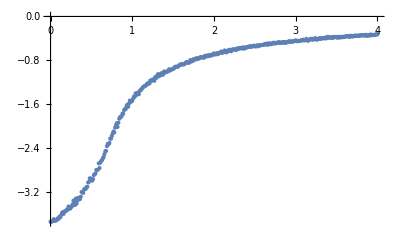

```mathematica
ListPlot[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,e/36^2}]
```

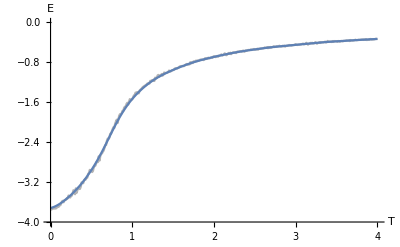

```mathematica
dataTandEWithFilter=Transpose@{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->e/36^2,20]};
Show[
ListPlot[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,e/36^2},AxesOrigin->{0,-4},PlotStyle->GrayLevel[0.7],AxesLabel->{"T","E"},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},Joined->True],
ListLinePlot[dataTandEWithFilter]
]
```

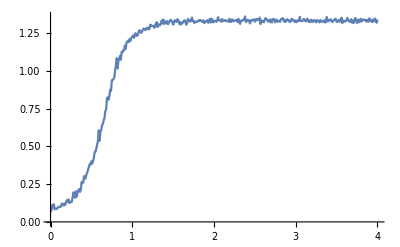

```mathematica
ListPlot[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,c},Joined->True]
```

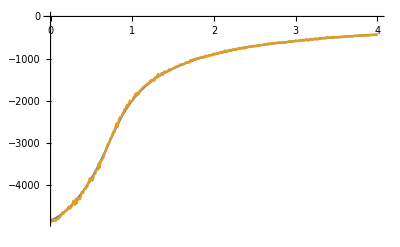

```mathematica
Transpose@{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->e,20]};
ListPlot[{%,data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,e}},Joined->True]
```

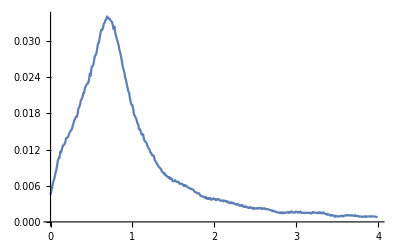

-Graphics-

```mathematica
Transpose@{data⟦;;-2⟧/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,Differences@GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->e/36^2,18]};
ListPlot[%,Joined->True]
Transpose@{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->e,20]};
ListPlot[{%,data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,e}},Joined->True]
```

```mathematica
interE=Interpolation[Transpose@{data⟦;;⟧/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->e/36^2,20]}]
```

InterpolatingFunction[{{0., 4.}}, <>]

```mathematica
D[interE[x],x]
```

InterpolatingFunction[{{0., 4.}}, <>][x]

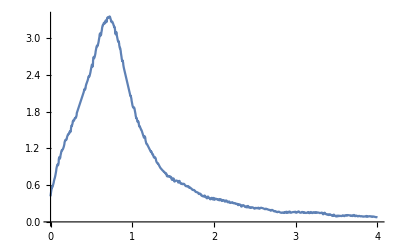

```mathematica
Plot[Evaluate@D[interE[x],x],{x,0.,4.}]
```

```mathematica
Show[
ListPlot[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,e/36^2},AxesOrigin->{0,-4},PlotStyle->GrayLevel[0.7],AxesLabel->{"T","E"},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},Joined->True],
ListLinePlot[dataTandEWithFilter]
]
```

Power::infy: 碰到无穷表达式 1/0^2.

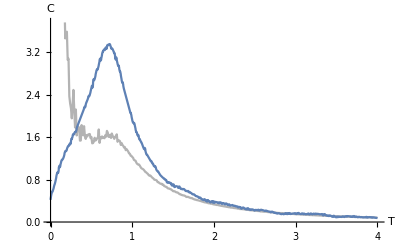

```mathematica
Show[
ListPlot[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,c/T^2},PlotStyle->GrayLevel[0.7],AxesLabel->{"T","C"},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},Joined->True],
Plot[Evaluate@D[interE[x],x],{x,0,4}]
]
```

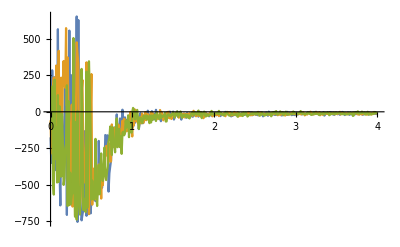

```mathematica
ListPlot[
{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,Mx},
data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,My},
data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,Mz}},
Joined->True,PlotRange->All]
```

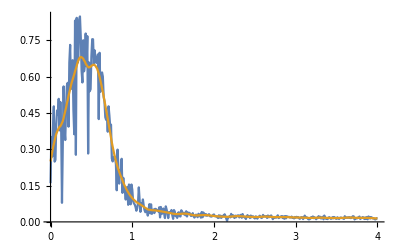

```mathematica
Transpose@{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->(√(Mx^2+My^2+Mz^2))/36^2,10]};
ListPlot[{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,(√(Mx^2+My^2+Mz^2))/36^2},%},Joined->True]
```

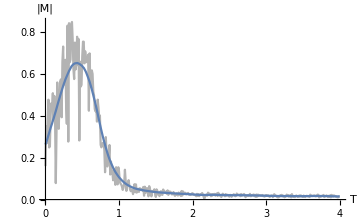

```mathematica
dataTandMWithFilter=Transpose@{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->(√(Mx^2+My^2+Mz^2))/36^2,20]};
Show[
ListPlot[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,(√(Mx^2+My^2+Mz^2))/36^2},PlotStyle->{GrayLevel[0.7](*,PointSize->Medium*)},AxesLabel->{"T","|M|"},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},Joined->True],
ListLinePlot[dataTandMWithFilter]
]
```

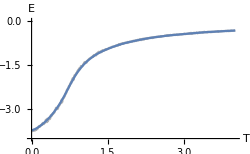
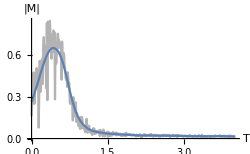

```mathematica
interM=Interpolation[dataTandMWithFilter];
```

Power::infy: 碰到无穷表达式 1/0.

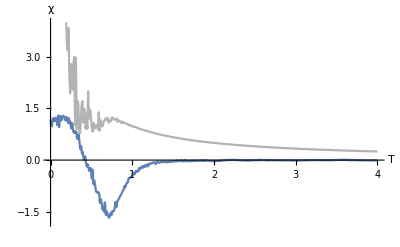

```mathematica
Show[
ListPlot[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,X/T},PlotRange->{-1.8,4},PlotStyle->GrayLevel[0.7],AxesLabel->{"T","χ"},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},Joined->True],
Plot[Evaluate@D[interM[x],x],{x,0,4},PlotRange->All]
]
```

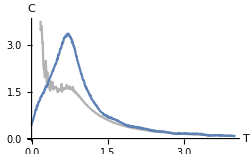
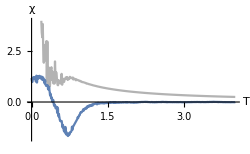

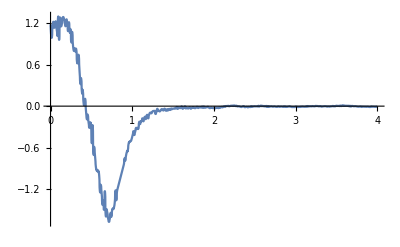

```mathematica
Plot[Evaluate@D[interM[x],x],{x,0,4},PlotRange->All]
```

Power::infy: 碰到无穷表达式 1/0.

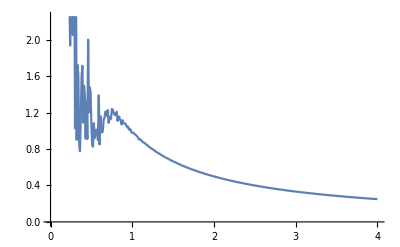

```mathematica
Transpose@{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->X/T,0]};
ListPlot[(*data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,X},*)%,Joined->True,PlotRange->Automatic]
```

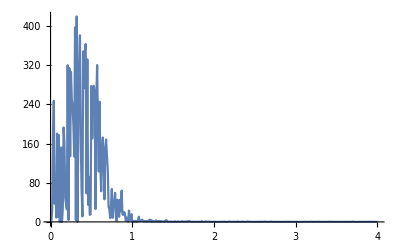

```mathematica
ListPlot[{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,Mz^2/36^2},%},Joined->True,PlotRange->All]
```

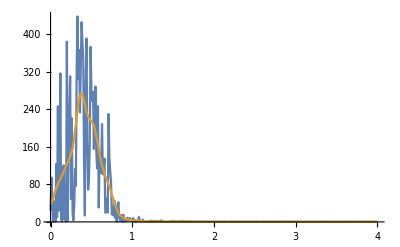

```mathematica
Transpose@{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->T,GaussianFilter[data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->Mx^2/36^2,10]};
ListPlot[{data/.{T_,J_,B_,d_,e_,Mx_,My_,Mz_,c_,X_,SD_}->{T,Mx^2/36^2},%},Joined->True,PlotRange->All]
```